```mathematica
alpha->  (p-alpha0)*(1+p^n)
```

alpha→(-alpha0+p) (1+p^n)

```mathematica
X-> -alpha*n*p^(n-1)/(1+p^n)^2
```

X→-(alpha n p^(-1+n))/((1+p^n)^2)

```mathematica
sol=3X^2/(4+2*X)/.X-> -alpha*n*p^(n-1)/(1+p^n)^2/.alpha->(p-alpha0)*(1+p^n)
```

(3 n^2 p^(-2+2 n) (-alpha0+p)^2)/((1+p^n)^2 (4-(2 n p^(-1+n) (-alpha0+p))/(1+p^n)))

```mathematica
sol1=sol/.alpha0-> 0/.n->2
```

(12 p^4)/((1+p^2)^2 (4-(4 p^2)/(1+p^2)))

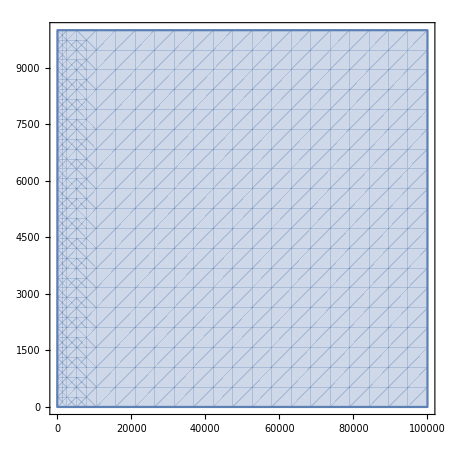

```mathematica
rp=RegionPlot[(beta+1)^2/beta<(12 p^4)/((1+p^2)^2 (4-(4 p^2)/(1+p^2))),{p,1,10^5},{beta,1,10^4}]
```

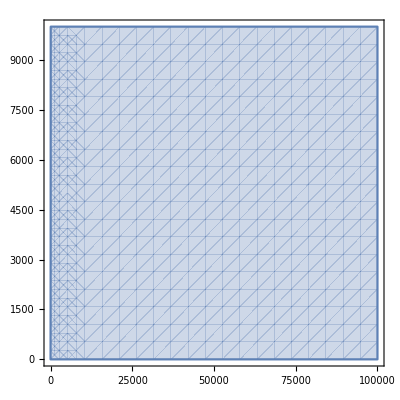
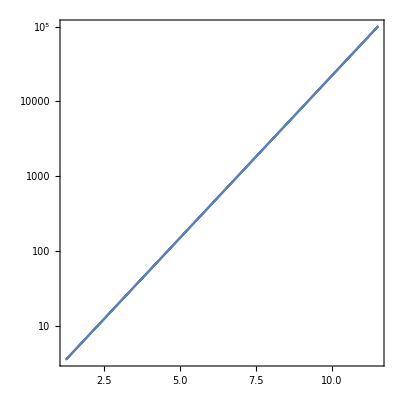

```mathematica
Row[{rp,Show[rp/.GraphicsComplex[c_,prims___]:>GraphicsComplex[{Log@#,Log@#}&@@@c,prims],FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Automatic,Automatic}},PlotRange->All]},Spacer[10]]
```

```mathematica
Clear["Global`*"]
```

```mathematica
alpha->  (p-alpha0)*(1+(p)^n)
```

alpha→(-alpha0+p) (1+p^n)

```mathematica
X-> -alpha*n*(p)^(n-1)/(1+(p)^n)^2
```

X→-(alpha n p^(-1+n))/((1+p^n)^2)

```mathematica
sol=3X^2/(4+2*X)/.X-> -alpha*n*(p)^(n-1)/(1+(p)^n)^2/.alpha->  (p-alpha0)*(1+(p)^n)
```

(3 n^2 p^(-2+2 n) (-alpha0+p)^2)/((1+p^n)^2 (4-(2 n p^(-1+n) (-alpha0+p))/(1+p^n)))

```mathematica
sol1=sol/.alpha0-> 0/.n->2.1
```

(13.23 p^4.2)/((1+p^2.1)^2 (4-(4.2 p^2.1)/(1+p^2.1)))

```mathematica
rp=RegionPlot[(beta+1)^2/beta<(13.23 p^4.2)/((1+p^2.1)^2 (4-(4.2 p^2.1)/(1+p^2.1))),{p,1,10^5},{beta,1,10^4}]
```

-Graphics-

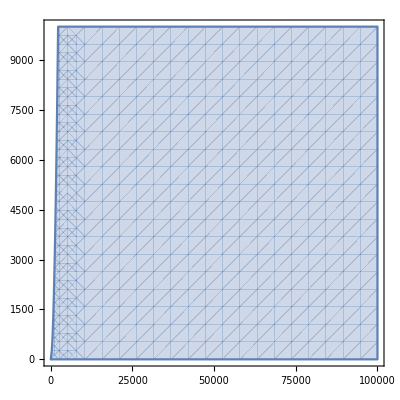
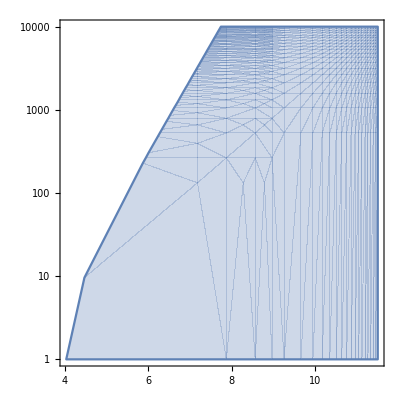

```mathematica
Row[{rp,Show[rp/.GraphicsComplex[c_,prims___]:>GraphicsComplex[{Log@#,Log@#2}&@@@c,prims],FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Automatic,Automatic}},PlotRange->All]},Spacer[10]]
```

```mathematica
FindInstance[x^2+y^2≤1,{x,y}]
```

```mathematica
FindInstance[(beta+1)^2/beta≤(12 p^4)/((1+p^2)^2 (4-(4 p^2)/(1+p^2))),{beta,p},500];
```

```mathematica
ListPlot[{beat,p},PlotRange->All]
```

-Graphics-